```mathematica
(* MacArthur-Rosenzweig Paradox of Enrichment *)
dRdt=b R (1-α R)-a R C/(1+a h R)
dCdt=e a R C/(1+a h R)-d C
```

-(a C R)/(1+a h R)+b R (1-R α)

-C d+(a C e R)/(1+a h R)

```mathematica
(* Solve for isoclines *)
isoR=Solve[dRdt==0,C]
isoC=Solve[dCdt==0,R]
```

{{C→-(b (1+a h R) (-1+R α))/a}}

{{R→d/(a (e-d h))}}

```mathematica
(* Solve for equilibria *)equil=Solve[{dRdt==0 ,dCdt==0},{R,C}]//FullSimplify;
equil//TableForm
```

R→0 | C→0
R→d/(a e-a d h) | C→(b e (a (e-d h)-d α))/(a^2 (e-d h)^2)
R→1/α | C→0

```mathematica
(*********************************************************************)
```

```mathematica
(* Define isocline(s) as function *)
fisoR[R_]=isoR[[1,1,2]]
fisoC=isoC[[1,1,2]]
```

-(b (1+a h R) (-1+R α))/a

d/(a (e-d h))

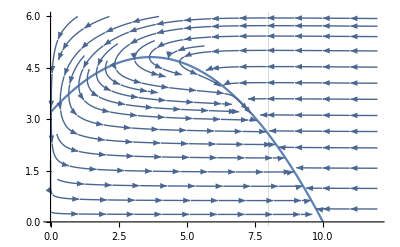

```mathematica
(* Provided parameter values and plot *)parms={b->0.8,α->0.1,a->0.25,e->0.1,h->1.5,d->0.05}; (* compare d->0.035 *)

Plot1=Plot[fisoR[R]/.parms,{R,0,12},GridLines->{{{fisoC/.parms,{Red,Thick}}},None},PlotRange->{All,{0,6}}];Plot2=StreamPlot[{dRdt,dCdt}/.parms,{R,0,12},{C,0,6}];
Show[Plot1,Plot2]
```

```mathematica
(* Provided parameter values and plot *)
Manipulate[

parms={b->B,α->Α,a->A,e->E,h->H,d->D};

Plot1=Plot[fisoR[R]/.parms,{R,0,12},GridLines->{{{fisoC/.parms,{Red,Thick}}},None},PlotRange->{All,{0,6}}];Plot2=StreamPlot[{dRdt,dCdt}/.parms,{R,0,12},{C,0,6}];
Show[Plot1,Plot2],

{{B,0.8,"b"},0.1,1},
{{Α,0.1,"α"},0.1,1},
{{A,0.25,"a"},0.1,1},
{{E,0.1,"e"},0.1,1},
{{H,1.5,"h"},0.1,3},
{{D,0.05,"d"},0.01,0.1}]
```